# Упражнение 1

```mathematica
f[x_]:=x*Sin[x]*Cos[x];
(*Полином на Тейлър от втора степен*)
Taylor2[x_,x0_]:=f[x0]+f'[x0](x-x0)+f''[x0](x-x0)^2/2!
(*Полином на Тейлър от трета степен*)
Taylor3[x_,x0_]:=Taylor2[x, x0]+f'''[x0](x-x0)^3/3!
(*Полином на Тейлър от четвърта степен*)
Taylor4[x_,x0_]:=Taylor3[x, x0]+f''''[x0](x-x0)^4/4!
```

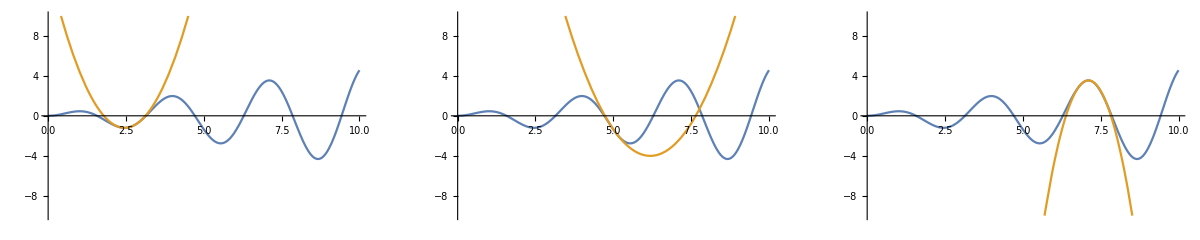

```mathematica
(*Апроксимация на f[x]=x*sin(x)*cos(x) в различни точки с полином от 2ра степен*)
GraphicsRow[
{Plot[{f[x],Taylor2[x,2.5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor2[x,5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor2[x,7]},{x,0,10},PlotRange->{{0,10},{-10,10}}]}
]
```

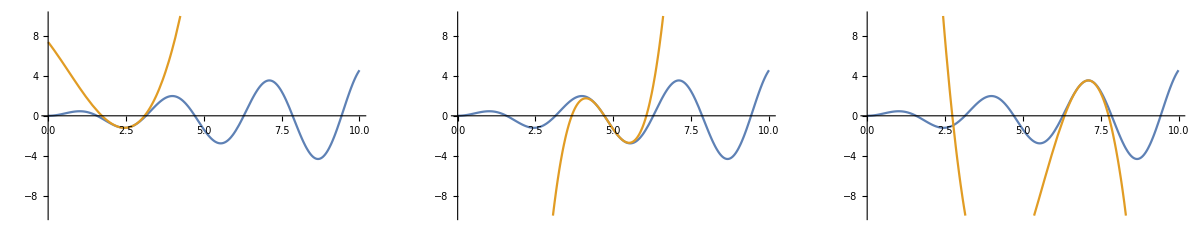

```mathematica
(*Апроксимация на f[x]=x*sin(x)*cos(x) в различни точки с полином от 3та степен*)
GraphicsRow[{Plot[{f[x],Taylor3[x,2.5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor3[x,5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor3[x,7]},{x,0,10},PlotRange->{{0,10},{-10,10}}]}]
```

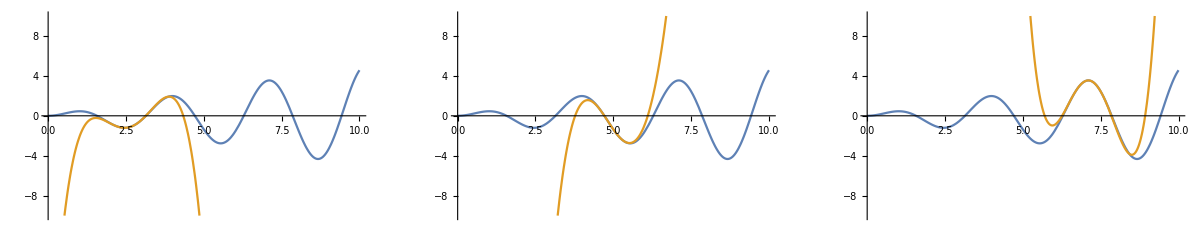

```mathematica
(*Апроксимация на f[x]=x*sin(x)*cos(x) в различни точки с полином от 4та степен*)
GraphicsRow[{Plot[{f[x],Taylor4[x,2.5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor4[x,5]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],Taylor4[x,7]},{x,0,10},PlotRange->{{0,10},{-10,10}}]}]
```

```mathematica
(*
Обща форма на полином на Тейлър
x0-Точка, около която се развива
order- Степен на полинома
*)
GeneralTaylor[x_,x0_,order_]:=(
Block[{y, result,i},
result=f[x0];
For[i=1,i≤order,++i,
result+=(((x-x0)^i)/i!)*D[f[y],{y,i}]
];
N[result/.y->x0]
]
)
```

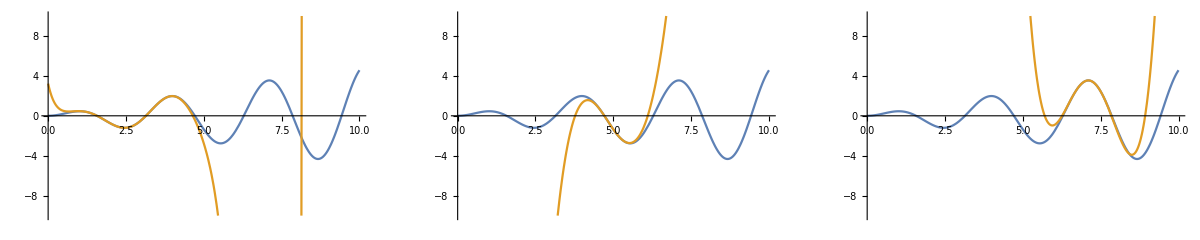

```mathematica
(*Апроксимация на f[x]=x*sin(x)*cos(x) в различни точки с полином от 10та степен*)
GraphicsRow[{Plot[{f[x],GeneralTaylor[x,2.5,10]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],GeneralTaylor[x,5,4]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],GeneralTaylor[x,7,4]},{x,0,10},PlotRange->{{0,10},{-10,10}}]}]
```

```mathematica
(*Намира коя е степентта на полинома на Тейлър, такава че, абсолютната стойност на абсолютната грешка да бъде по-малка от err във всяка една точка*)
GetOrder[err_,maxOrder_]:=(
Block[{order,x,maxErr},
For[order=1,order≤maxOrder,++order,
maxErr=N[MaxValue[Abs[f[x]-GeneralTaylor[x,5,order]],0≤x≤10,x]];
Print["Max Error: ",maxErr," order: ",order];
If[maxErr≤err,
Return[order]
]
]
]
)
```

## Задача 2

```mathematica
ClearAll["Global`*"]
f[x_]:=E^x
forward[x_,dt_]:=(f[x+dt]-f[x])/dt
backward[x_,dt_]:=(f[x]-f[x-dt])/dt
central[x_,dt_]:=(f[x+dt]-f[x-dt])/(2dt)
```

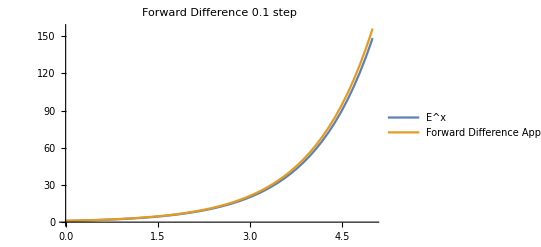

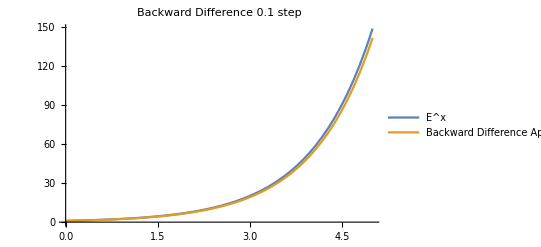

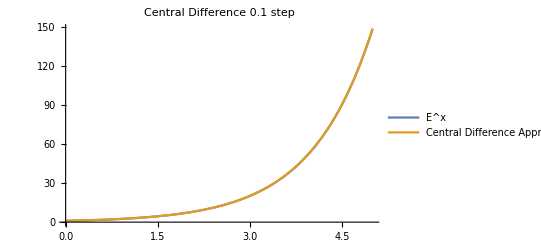

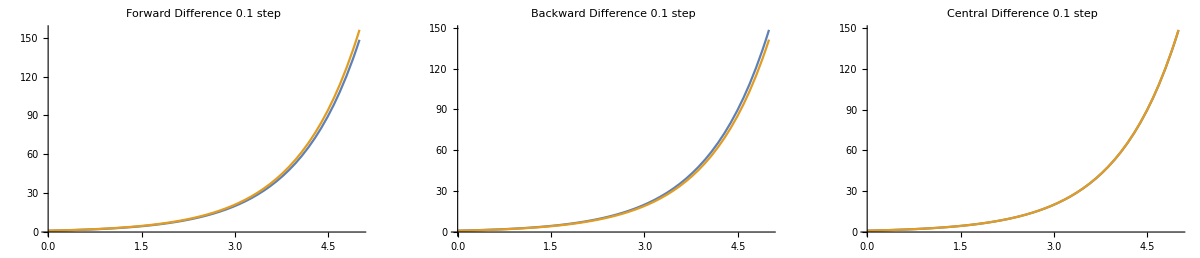

```mathematica
Print[Plot[{f[x],forward[x,0.1]},{x,0,5},PlotLabel->"Forward Difference 0.1 step",PlotLegends->{"E^x","Forward Difference Approximation"}]];
Print[Plot[{f[x],backward[x,0.1]},{x,0,5},PlotLabel->"Backward Difference 0.1 step",PlotLegends->{"E^x","Backward Difference Approximation"}]];
Print[Plot[{f[x],central[x,0.1]},{x,0,5},PlotLabel->"Central Difference 0.1 step",PlotLegends->{"E^x","Central Difference Approximation"}]];
Print[GraphicsRow[{
Plot[{f[x],forward[x,0.1]},{x,0,5},PlotLabel->"Forward Difference 0.1 step"],
Plot[{f[x],backward[x,0.1]},{x,0,5},PlotLabel->"Backward Difference 0.1 step"],
Plot[{f[x],central[x,0.1]},{x,0,5},PlotLabel->"Central Difference 0.1 step"]
}]];
```

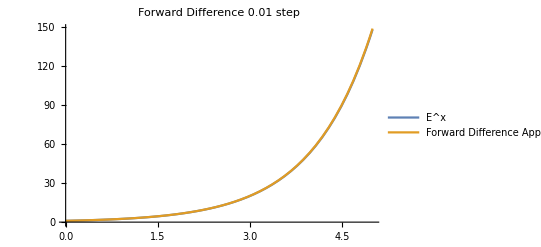

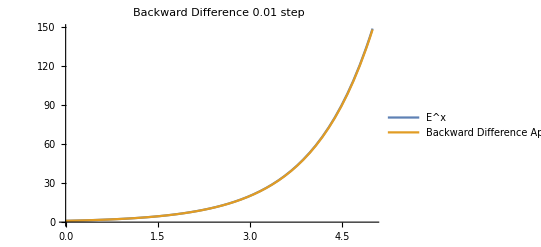

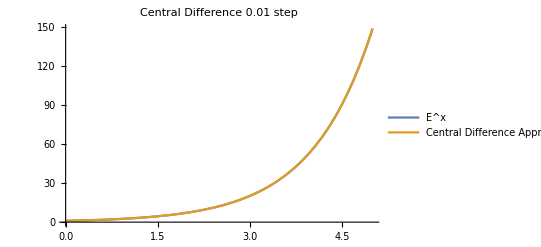

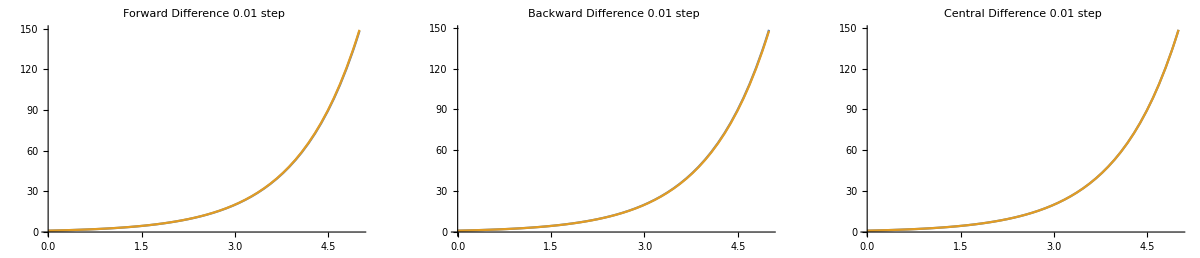

```mathematica
Print[Plot[{f[x],forward[x,0.01]},{x,0,5},PlotLabel->"Forward Difference 0.01 step",PlotLegends->{"E^x","Forward Difference Approximation"}]];
Print[Plot[{f[x],backward[x,0.01]},{x,0,5},PlotLabel->"Backward Difference 0.01 step",PlotLegends->{"E^x","Backward Difference Approximation"}]];
Print[Plot[{f[x],central[x,0.01]},{x,0,5},PlotLabel->"Central Difference 0.01 step",PlotLegends->{"E^x","Central Difference Approximation"}]];
Print[GraphicsRow[{
Plot[{f[x],forward[x,0.01]},{x,0,5},PlotLabel->"Forward Difference 0.01 step"],
Plot[{f[x],backward[x,0.01]},{x,0,5},PlotLabel->"Backward Difference 0.01 step"],
Plot[{f[x],central[x,0.01]},{x,0,5},PlotLabel->"Central Difference 0.01 step"]
}]];
```

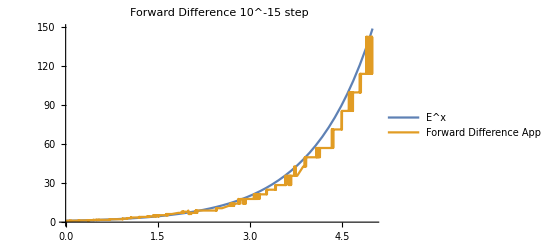

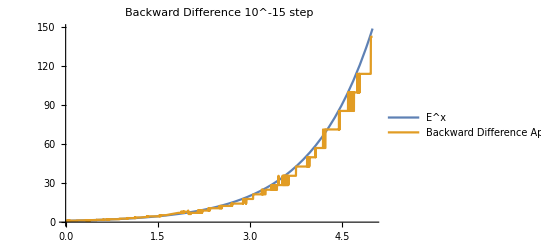

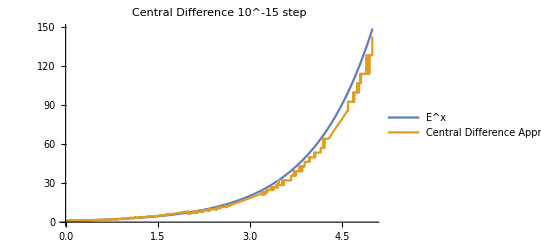

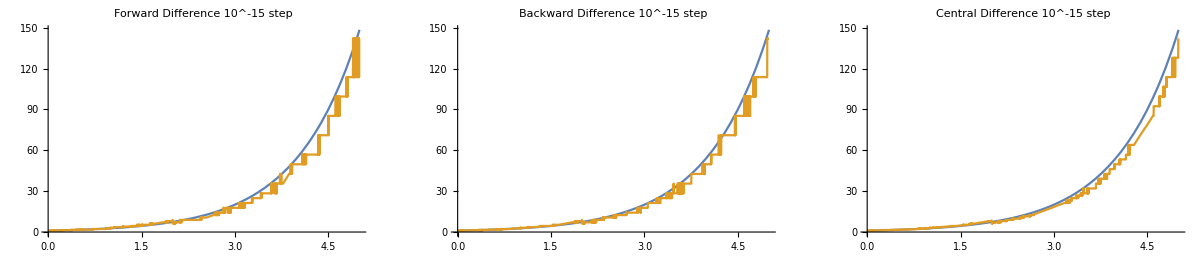

```mathematica
Print[Plot[{f[x],forward[x,10^-15]},{x,0,5},PlotLabel->"Forward Difference 10^-15 step",PlotLegends->{"E^x","Forward Difference Approximation"}]];
Print[Plot[{f[x],backward[x,10^-15]},{x,0,5},PlotLabel->"Backward Difference 10^-15 step",PlotLegends->{"E^x","Backward Difference Approximation"}]];
Print[Plot[{f[x],central[x,10^-15]},{x,0,5},PlotLabel->"Central Difference 10^-15 step",PlotLegends->{"E^x","Central Difference Approximation"}]];
Print[GraphicsRow[{
Plot[{f[x],forward[x,10^-15]},{x,0,5},PlotLabel->"Forward Difference 10^-15 step"],
Plot[{f[x],backward[x,10^-15]},{x,0,5},PlotLabel->"Backward Difference 10^-15 step"],
Plot[{f[x],central[x,10^-15]},{x,0,5},PlotLabel->"Central Difference 10^-15 step"]
}]];
```

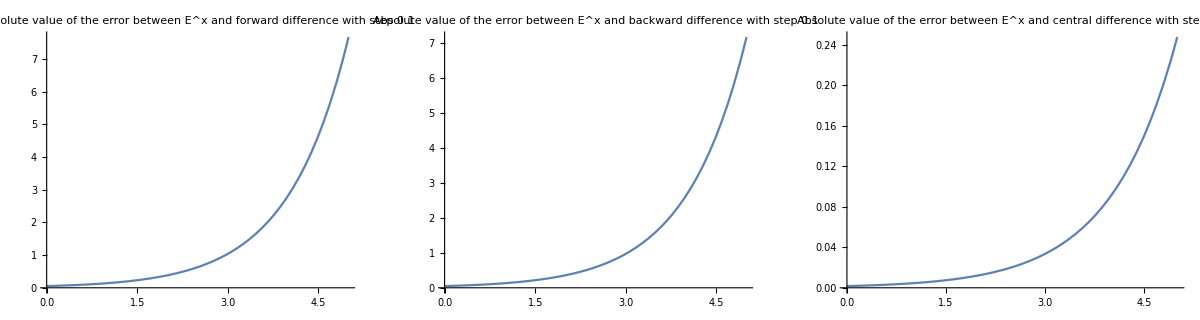

```mathematica
Print[GraphicsRow[{
Plot[Abs[f[x]-forward[x,0.1]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and forward difference with step 0.1"],
Plot[Abs[f[x]-backward[x,0.1]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and backward difference with step 0.1"],
Plot[Abs[f[x]-central[x,0.1]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and central difference with step 0.1"]
}]];
```

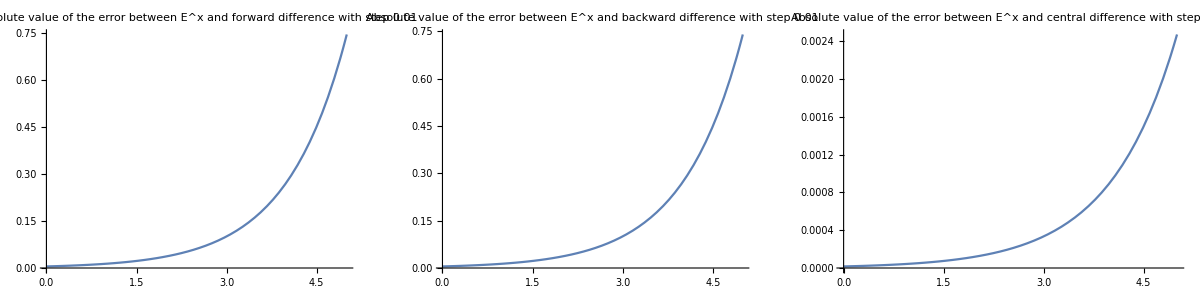

```mathematica
Print[GraphicsRow[{
Plot[Abs[f[x]-forward[x,0.01]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and forward difference with step 0.01"],
Plot[Abs[f[x]-backward[x,0.01]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and backward difference with step 0.01"],
Plot[Abs[f[x]-central[x,0.01]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and central difference with step 0.01"]
}]];
```

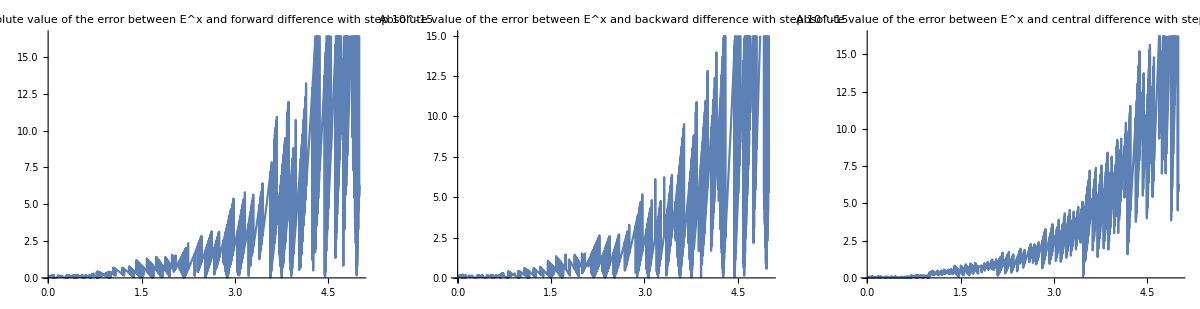

```mathematica
Print[GraphicsRow[{
Plot[Abs[f[x]-forward[x,10^-15]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and forward difference with step 10^-15"],
Plot[Abs[f[x]-backward[x,10^-15]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and backward difference with step 10^-15"],
Plot[Abs[f[x]-central[x,10^-15]],{x,0,5},PlotLabel->"Absolute value of the error between E^x\n and central difference with step 10^-15"]
}]];
```